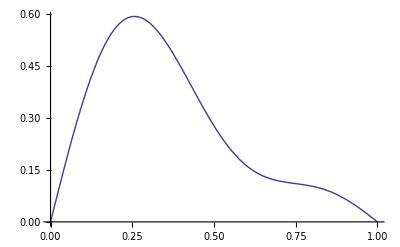

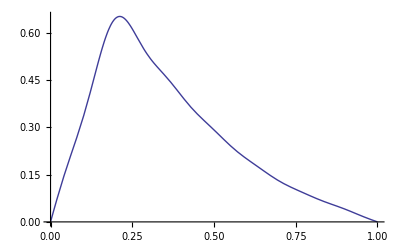

```mathematica
Clear["Global`*"]
u0[x_]:=x(1-x);
u1[x_] := x;
a[n_,l_]:=2/l∫_0^l u0[x]Sin[(n Pi x)/l]ⅆx;
b[n_,l_]:=2/l∫_0^l u1[x]Sin[(n Pi x)/l]ⅆx;
u[N_,x_,t_,l_,c_]:=∑_(n=1)^N Sin[(n Pi x)/l](a[n,l]Cos[(n Pi c)/l t] + l/(n Pi c)b[n,l]Sin[(n Pi c)/l t]);
graphu[N_,t_,l_,c_]:= Plot[Evaluate[u[N,x,t,l,c]],{x,0,l},PlotRange->All];
graphu[3,4,1.0,.2]
graphu[15,4,1.0,.2]
```

```mathematica
b[n,1]//FullSimplify
```

(2 (-n π Cos[n π]+Sin[n π]))/(n^2 π^2)

```mathematica
FullSimplify[a[n,1]]
```

(4-4 Cos[n π]-2 n π Sin[n π])/(n^3 π^3)